```mathematica
μm=10^-6;
c=299792458;
fs=10^-15;
mm=10^-3;
nm=10^-9;
```

Refractive index. Ref: refractiveindex.info

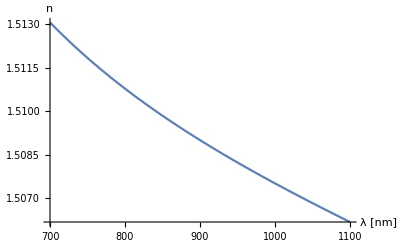

```mathematica
nsi[λ_]:=(1+(0.6961663 (λ/μm)^2)/((λ/μm)^2-0.0684043^2)+(0.4079426(λ/μm)^2)/((λ/μm)^2-0.1162414^2)+(0.8974794(λ/μm)^2)/((λ/μm)^2-9.896161^2))^(1/2)(*fused silica*)
nBK7[λ_]:=(1+(1.03961212  (λ/μm)^2)/((λ/μm)^2-0.00600069867)+(0.231792344(λ/μm)^2)/((λ/μm)^2-0.0200179144)+(1.01046945(λ/μm)^2)/((λ/μm)^2-103.560653))^(1/2)(*N-BK7*)
Plot[nBK7[λ nm],{λ,700,1100},AxesLabel->{"λ [nm]","n"}]
```

Group velocity dispersion (GVD). Ref: Young 2015 and Newport website

```mathematica
GVDBK7[λ_]:=(λ^3 nBK7''[λ])/(2π c^2)
GVDsi[λ_]:=(λ^3 nsi''[λ])/(2π c^2)
GDD[L_,f_]:=L*f(*Group delay dispersion GDD = GVD*L, where L is the material thickness*)
```

Group delay dispersion GDD vs wavelength

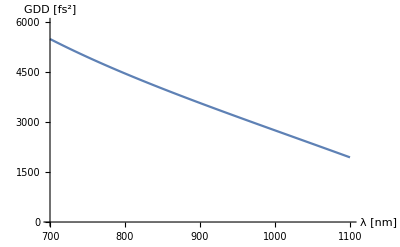

```mathematica
Plot[GDD[100mm,GVDBK7[λ nm]]/fs^2,{λ,700,1100},PlotRange->{0,6000},AxesLabel->{"λ [nm]","GDD [fs^2]"}]
```

Gaussian pulse broadening
Ref: Eq8 in http://www.newport.com/The-Effect-of-Dispersion-on-Ultrashort-Pulses/602091/1033/content.aspx

```mathematica
Δtout[Δt_,GDD_]:=(√(Δt^4+16 Log[2]^2 GDD^2))/Δt
```

Output vs input pulse width (gaussian pulse)

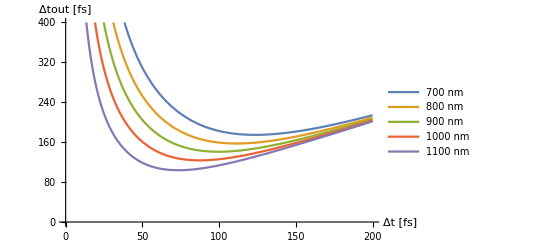

```mathematica
Plot[Evaluate[Table[Δtout[Δt fs,GDD[100mm,GVDBK7[λ nm]]]/fs,{λ,700,1100,100}]],{Δt,0,200},PlotRange->{0,400},AxesLabel->{"Δt [fs]","Δtout [fs]"},PlotLegends->{"700 nm","800 nm","900 nm","1000 nm","1100 nm"}]
```

Output pulse width vs material thickness

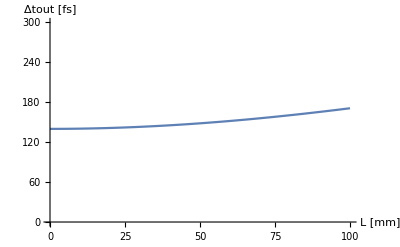

```mathematica
Plot[Evaluate[Δtout[140fs,GDD[L mm,GVDBK7[750nm]]]/fs],{L,0,100},PlotRange->{0,300},AxesLabel->{"L [mm]","Δtout [fs]"}]
```